# Maximizing Peak Area (and Peak Height)

## Eric Moyer

June 2013

## Introduction

In order to make the sampled distributions more accurate and avoid missing generated peak parameter values, I will augment the sampled distributions by setting the their maxima and minima to the true maxima and minima.

Peak height is generated by first selecting heights from a known distribution and then dividing them by the highest point in the resulting noiseless spectrum.

Peak areas are generated by a simple nonlinear formula (that is essentially a scaled product of the parameters). In hindsight (I am writing this introduction after doing the work) it should have been obvious that the maximum area came when you took the maximum of the two main parameters and let P be 1 (since  π>√(π/(log(2))))

## Work

### Calculate max area and max height

Formula for the area of a peak with the given height (M) width at half height (G) and Lorentzianness (P).

```mathematica
area[M_,G_,P_]:=(1/2) M G (P Pi+(1-P) Sqrt[Pi/Log[2]])
```

Take the first derivative with respect to each variable (glad I took Calc 3 :)

```mathematica
D[area[M,G,P],{{M,G,P}}]
```

{1/2 G (P π+(1-P) √(π/Log[2])),1/2 M (P π+(1-P) √(π/Log[2])),1/2 G M (π-√(π/Log[2]))}=={0,0,0}

Find the zeros of the derivative.

```mathematica
Solve[{1/2 G (P π+(1-P) √(π/Log[2]))==0,1/2 M (P π+(1-P) √(π/Log[2]))==0,1/2 G M (π-√(π/Log[2]))==0},{M,G,P}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{G→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))},{G→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))},{M→0,G→0},{M→0,G→0},{M→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))},{M→0,P→(√(π/Log[2]))/(-π+√(π/Log[2]))}}

The only unconstrained optima are where the area is 0. Double check using Mathematica's maximize routine.

```mathematica
Maximize[area[M,G,P],{M,G,P}]
```

Maximize::natt: The maximum is not attained at any point satisfying the given constraints.

{∞,{M→-∞,G→-1,P→0}}

Now, look at the maxima where the height, width, and lorentzianness are constrained by the values from the original distributions.

Range of Lorentzianness: 0..1

Range of width-at-half-height:  [0.00172017711207981768, 0.0449550522830431884]

Range of height is more complicated because the heights in any spectrum are divided by the height of the highest point in that spectrum. The maximum height is 1 (put all the other peaks as far away as possible and make them as small as possible and their contribution to the largest peak will be negligable.) The minimum is the smallest original height divided by its height plus 6 times the largest original height (put all the peaks at one place and make 6 of them be maximum size.

Unscaled height range: [ 0.000191973000000000013, 1.99409999999999998 ]

min / (6*max + min):

```mathematica
maxOrigHeight =199409999999999998/100000000000000000
```

99704999999999999/50000000000000000

```mathematica
minOrigHeight=191973000000000013/1000000000000000000000
```

191973000000000013/1000000000000000000000

```mathematica
scaledMinHeight=minOrigHeight/(6*maxOrigHeight+minOrigHeight)
```

191973000000000013/11964791972999999880013

```mathematica
N[scaledMinHeight,28]
```

0.00001604482555427710777509984241

So, the range for scaled heights is: [ 0.00001604482555427710777509984241, 1 ]

```mathematica
Maximize[{area[M,G,P],0≤P≤1,scaledMinHeight≤M≤1,0.00172017711207981768≤G≤0.0449550522830431884},{M,G,P}]
```

{0.070615230997076772,{M→1.,G→0.04495505228304319,P→1.}}

Maximum area is attained by letting all the M,G, and P have their maximum values.

### Double-check assumption that height contribution of 6 distant small peaks is negligable

Width of most congested spectrum: 0.0260837320427020625

Function for Gauss-Lorentz Peak:

```mathematica
lorentzian[G_,x_,x0_]:=(G^2)/(4(x-x0)^2+G^2)
```

```mathematica
gaussian[G_,x_,x0_]:=Exp[-(x-x0)^2/(2 (G/2 Sqrt[2 Log[2]])^2)]
```

```mathematica
glp[M_,G_,P_,x_,x0_]:=M(P lorentzian[G,x,x0]+(1-P) gaussian[G,x,x0])
```

Make sure it looks right

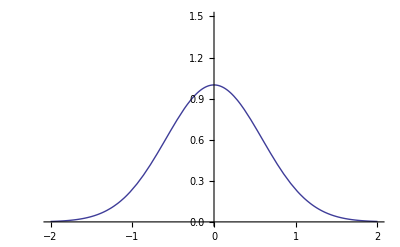

```mathematica
Plot[glp[1,1,0,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

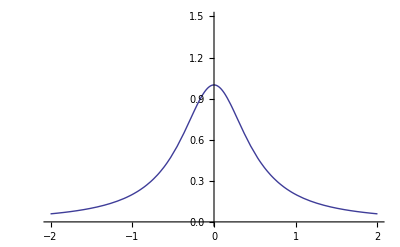

```mathematica
Plot[glp[1,1,1,x,0],{x,-2,2},PlotRange->{0,1.5}]
```

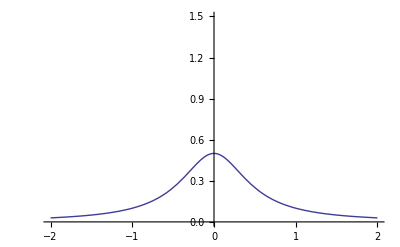

```mathematica
Plot[glp[0.5,1,1,x,0],{x,-2,2},PlotRange->{0,1.5}]
```